# Optimizing QSAR with DFT Variables

#### A validation of the Results from Aouidate, et al. “Combining DFT and QSAR studies for predicting psychotomimeticactivity of substituted phenethylamines using statistical methods.” Journal of Taibah University for Science 10 (2016): 787-96.

## Background

The medicinal value of drugs is optimized via Quantitative Structure-Activity Relationships, or QSAR. QSAR seeks to explain the variation in the biological activity of related molecules via variations in their structure and physicochemical properties. Synthesizing and testing new compounds is time-consuming and expensive, so the faster we can reach a mathematical model with predictive power, the better. The physicochemical properties of compounds used in such studies are ultimately a function of the compounds’ electronic structure. The electronic structure of molecules can be computed using Density Functional Theory, or DFT. This is a computationally intensive process, but newer software is becoming more efficient and accessible. Aouidate, et al collected from the literature the biochemical activities of 46 phenalkylamines, a frequently-abused class of psychoactive drugs. They calculated the DFT parameters Etotal, Ehomo, Elumo, dipole moment (DM), and absolute hardness (η), and physicochemical properties such as molecular weight, density, and octanol/water partition coefficient (logP). For phenalkylamines, biological activity is expressed in Mescaline Units (logUM).

## Code

### Importing Data

```mathematica
dataFile=FileNameJoin[{NotebookDirectory[],"Table of Aouidate data.xlsx"}]
```

/Users/themarchhare/Documents/Mathematica Seminar/Table of Aouidate data.xlsx

```mathematica
data1=Import[dataFile]
```

{{{logUM,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP},{2.72,−82328.726,7.374,−5.682,5.522,−0.160,3.242,0.046,−0.707,274.154,1.54,37.9,1.324,2.455},{1.96,−30241.000,7.125,−5.428,5.258,−0.170,1.996,0.135,−0.708,255.376,1.545,42.6,1.08,2.452},{2.02,−19406.400,6.731,−5.029,5.302,0.273,1.234,0.126,−0.712,223.311,1.509,33.9,0.998,2.778},{1.95,−20476.100,6.724,−5.037,5.295,0.258,1.283,0.126,−0.709,237.338,1.507,33.9,0.998,3.307},{1.9,−18336.700,6.765,−5.009,5.282,0.273,1.117,0.127,−0.710,209.285,1.511,34.2,1.01,2.249},{1.71,−31310.656,7.238,−4.780,5.066,0.286,2.498,−0.150,−0.712,269.403,1.539,41.2,1.07,2.761},{1.69,−86156.656,7.374,−5.687,5.527,−0.160,3.271,0.046,−0.709,260.128,1.548,39.5,1.368,2.146},{1.68,−21545.885,6.721,−5.025,5.3,0.275,1.25,0.122,−0.713,251.365,1.504,33.9,0.979,3.386},{1.66,−29171.207,7.121,−5.453,5.295,−0.158,2.115,−0.131,−0.707,241.35,1.55,43.1,1.1,1.923},{1.36,−29171.025,6.993,−5.327,5.234,−0.093,4.017,−0.219,−0.713,241.35,1.552,44.2,1.1,1.743},{1.33,−20382.821,6.83,−5.101,5.576,0.475,3.159,0.349,−0.713,225.284,1.507,34.3,1.048,1.392},{1.25,−18336.601,6.802,−5.024,5.301,0.278,1.323,0.125,−0.716,209.285,1.514,34.9,1.012,2.469},{1.29,−30240.922,7.156,−5.333,5.236,−0.097,4.084,−0.220,−0.707,255.376,1.547,43.6,1.09,2.272},{1.27,−17266.813,8.353,−5.142,5.451,0.309,1.618,0.133,−0.714,195.258,1.516,35.3,1.026,1.94},{1.14,−22396.415,7.075,−5.349,5.755,0.407,1.297,0.273,−0.713,239.268,1.54,43.5,1.184,1.644},{1.36,−21452.636,6.803,−5.073,5.531,0.458,3.234,0.353,−0.707,239.311,1.504,34.3,1.034,1.921},{1.11,−28101.400,7.292,−5.423,5.335,−0.088,4.378,−0.223,−0.708,227.323,1.559,45.,1.12,1.214},{1.,−19280.462,7.265,−5.393,5.876,0.483,1.539,0.326,−0.707,209.242,1.55,45.4,1.175,1.699},{1.05,−21452.636,7.265,−5.505,5.911,0.406,3.041,0.265,−0.713,239.311,1.504,34.3,1.034,1.571},{1.,−19280.543,6.803,−4.968,5.226,0.258,1.505,0.326,−0.715,209.242,1.55,45.4,1.175,1.699},{1.38,−22522.370,6.911,−5.063,5.528,0.465,3.276,0.352,−0.713,253.337,1.502,34.2,1.022,2.45},{0.87,−20382.821,7.265,−5.505,5.908,0.403,3.089,0.225,−0.714,225.284,1.508,35.2,1.05,1.262},{0.86,−23498.638,7.374,−5.703,5.961,0.257,1.288,0.269,−0.714,255.31,1.503,34.,1.069,0.637},{0.83,−21452.500,7.183,−5.443,5.831,0.389,2.994,0.264,−0.714,239.311,1.506,35.1,1.036,−1.842},{0.84,−29171.025,7.129,−5.499,5.468,−0.030,3.92,0.293,−0.712,241.35,1.552,44.2,1.1,1.248},{0.84,−29171.025,7.102,−5.569,5.499,−0.070,3.714,0.289,−0.708,241.35,1.552,44.2,1.1,−1.003},{0.81,−28101.400,7.319,−5.536,5.488,−0.049,4.009,0.293,−0.702,227.323,1.559,45.,1.12,0.719},{0.76,−22396.388,7.02,−5.281,5.594,0.313,0.427,0.283,−0.702,239.268,1.54,43.5,1.184,1.294},{0.66,−29171.025,7.047,−5.407,5.332,−0.075,4.42,−0.226,−0.705,241.35,1.552,44.2,1.1,1.743},{0.68,−30240.922,7.02,−5.303,5.221,−0.082,4.043,−0.222,−0.713,255.376,1.547,43.6,1.09,2.272},{0.67,−17266.922,7.047,−5.243,5.765,0.522,2.553,0.378,−0.713,195.258,1.512,34.7,1.023,−1.265},{0.59,−12104.477,7.809,−5.971,6.34,0.37,1.567,0.179,−0.707,149.233,1.525,35.2,0.938,2.241},{0.58,−31310.547,7.02,−5.311,5.224,−0.088,4.067,−0.219,−0.712,269.403,1.543,43.1,1.07,2.801},{0.46,−26669.745,7.238,−5.590,5.669,0.079,3.375,0.267,−0.712,301.38,1.555,39.8,1.093,2.81},{0.43,−19280.462,7.211,−5.328,5.872,0.544,1.369,0.265,−0.713,209.242,1.55,45.4,1.175,1.699},{0.41,−16164.481,7.211,−5.293,5.602,0.309,1.899,0.329,−0.708,179.216,1.564,48.,1.163,1.707},{0.38,−22522.234,7.156,−5.435,5.827,0.391,2.947,0.265,−0.713,253.337,1.503,35.,1.023,1.777},{0.38,−30240.922,7.02,−5.247,5.533,0.286,3.05,0.3,−0.711,255.376,1.547,43.6,1.09,1.777},{0.38,−30240.922,7.156,−5.533,5.466,−0.067,3.751,0.285,−0.710,255.376,1.547,43.6,1.09,1.777},{0.33,−20382.766,7.319,−5.524,5.912,0.388,3.136,0.245,−0.719,225.284,1.507,34.3,1.048,1.042},{0.23,−21452.609,7.129,−5.410,5.794,0.384,2.979,0.26,−0.713,239.311,1.506,35.1,1.036,1.273},{0.03,−20382.739,7.238,−5.481,5.872,0.39,3.237,0.249,−0.713,225.284,1.508,35.2,1.05,0.744},{0.,−19312.923,7.319,−5.523,5.914,0.391,3.203,0.253,−0.707,211.258,1.511,35.4,1.067,0.215},{−0.030,−19312.787,7.456,−5.719,6.007,0.288,1.449,0.305,−0.710,211.258,1.511,35.4,1.067,−3.080},{−0.060,−17266.759,7.292,−5.444,5.849,0.405,3.673,0.308,−0.717,195.258,1.512,34.7,1.023,0.435},{−0.670,−16196.943,7.292,−5.443,5.848,0.406,3.724,0.307,−0.713,181.232,1.517,36.,1.041,0.126},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,}},{{,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,γ,D,logP,logUM},{,1.,,3.,,5.,6.,,,,10.,,,}}}

```mathematica
firstSheet1=Part[data1,1]
(*displaying the order of the variable columns for future reference*)
```

{{logUM,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP},{2.72,−82328.726,7.374,−5.682,5.522,−0.160,3.242,0.046,−0.707,274.154,1.54,37.9,1.324,2.455},{1.96,−30241.000,7.125,−5.428,5.258,−0.170,1.996,0.135,−0.708,255.376,1.545,42.6,1.08,2.452},{2.02,−19406.400,6.731,−5.029,5.302,0.273,1.234,0.126,−0.712,223.311,1.509,33.9,0.998,2.778},{1.95,−20476.100,6.724,−5.037,5.295,0.258,1.283,0.126,−0.709,237.338,1.507,33.9,0.998,3.307},{1.9,−18336.700,6.765,−5.009,5.282,0.273,1.117,0.127,−0.710,209.285,1.511,34.2,1.01,2.249},{1.71,−31310.656,7.238,−4.780,5.066,0.286,2.498,−0.150,−0.712,269.403,1.539,41.2,1.07,2.761},{1.69,−86156.656,7.374,−5.687,5.527,−0.160,3.271,0.046,−0.709,260.128,1.548,39.5,1.368,2.146},{1.68,−21545.885,6.721,−5.025,5.3,0.275,1.25,0.122,−0.713,251.365,1.504,33.9,0.979,3.386},{1.66,−29171.207,7.121,−5.453,5.295,−0.158,2.115,−0.131,−0.707,241.35,1.55,43.1,1.1,1.923},{1.36,−29171.025,6.993,−5.327,5.234,−0.093,4.017,−0.219,−0.713,241.35,1.552,44.2,1.1,1.743},{1.33,−20382.821,6.83,−5.101,5.576,0.475,3.159,0.349,−0.713,225.284,1.507,34.3,1.048,1.392},{1.25,−18336.601,6.802,−5.024,5.301,0.278,1.323,0.125,−0.716,209.285,1.514,34.9,1.012,2.469},{1.29,−30240.922,7.156,−5.333,5.236,−0.097,4.084,−0.220,−0.707,255.376,1.547,43.6,1.09,2.272},{1.27,−17266.813,8.353,−5.142,5.451,0.309,1.618,0.133,−0.714,195.258,1.516,35.3,1.026,1.94},{1.14,−22396.415,7.075,−5.349,5.755,0.407,1.297,0.273,−0.713,239.268,1.54,43.5,1.184,1.644},{1.36,−21452.636,6.803,−5.073,5.531,0.458,3.234,0.353,−0.707,239.311,1.504,34.3,1.034,1.921},{1.11,−28101.400,7.292,−5.423,5.335,−0.088,4.378,−0.223,−0.708,227.323,1.559,45.,1.12,1.214},{1.,−19280.462,7.265,−5.393,5.876,0.483,1.539,0.326,−0.707,209.242,1.55,45.4,1.175,1.699},{1.05,−21452.636,7.265,−5.505,5.911,0.406,3.041,0.265,−0.713,239.311,1.504,34.3,1.034,1.571},{1.,−19280.543,6.803,−4.968,5.226,0.258,1.505,0.326,−0.715,209.242,1.55,45.4,1.175,1.699},{1.38,−22522.370,6.911,−5.063,5.528,0.465,3.276,0.352,−0.713,253.337,1.502,34.2,1.022,2.45},{0.87,−20382.821,7.265,−5.505,5.908,0.403,3.089,0.225,−0.714,225.284,1.508,35.2,1.05,1.262},{0.86,−23498.638,7.374,−5.703,5.961,0.257,1.288,0.269,−0.714,255.31,1.503,34.,1.069,0.637},{0.83,−21452.500,7.183,−5.443,5.831,0.389,2.994,0.264,−0.714,239.311,1.506,35.1,1.036,−1.842},{0.84,−29171.025,7.129,−5.499,5.468,−0.030,3.92,0.293,−0.712,241.35,1.552,44.2,1.1,1.248},{0.84,−29171.025,7.102,−5.569,5.499,−0.070,3.714,0.289,−0.708,241.35,1.552,44.2,1.1,−1.003},{0.81,−28101.400,7.319,−5.536,5.488,−0.049,4.009,0.293,−0.702,227.323,1.559,45.,1.12,0.719},{0.76,−22396.388,7.02,−5.281,5.594,0.313,0.427,0.283,−0.702,239.268,1.54,43.5,1.184,1.294},{0.66,−29171.025,7.047,−5.407,5.332,−0.075,4.42,−0.226,−0.705,241.35,1.552,44.2,1.1,1.743},{0.68,−30240.922,7.02,−5.303,5.221,−0.082,4.043,−0.222,−0.713,255.376,1.547,43.6,1.09,2.272},{0.67,−17266.922,7.047,−5.243,5.765,0.522,2.553,0.378,−0.713,195.258,1.512,34.7,1.023,−1.265},{0.59,−12104.477,7.809,−5.971,6.34,0.37,1.567,0.179,−0.707,149.233,1.525,35.2,0.938,2.241},{0.58,−31310.547,7.02,−5.311,5.224,−0.088,4.067,−0.219,−0.712,269.403,1.543,43.1,1.07,2.801},{0.46,−26669.745,7.238,−5.590,5.669,0.079,3.375,0.267,−0.712,301.38,1.555,39.8,1.093,2.81},{0.43,−19280.462,7.211,−5.328,5.872,0.544,1.369,0.265,−0.713,209.242,1.55,45.4,1.175,1.699},{0.41,−16164.481,7.211,−5.293,5.602,0.309,1.899,0.329,−0.708,179.216,1.564,48.,1.163,1.707},{0.38,−22522.234,7.156,−5.435,5.827,0.391,2.947,0.265,−0.713,253.337,1.503,35.,1.023,1.777},{0.38,−30240.922,7.02,−5.247,5.533,0.286,3.05,0.3,−0.711,255.376,1.547,43.6,1.09,1.777},{0.38,−30240.922,7.156,−5.533,5.466,−0.067,3.751,0.285,−0.710,255.376,1.547,43.6,1.09,1.777},{0.33,−20382.766,7.319,−5.524,5.912,0.388,3.136,0.245,−0.719,225.284,1.507,34.3,1.048,1.042},{0.23,−21452.609,7.129,−5.410,5.794,0.384,2.979,0.26,−0.713,239.311,1.506,35.1,1.036,1.273},{0.03,−20382.739,7.238,−5.481,5.872,0.39,3.237,0.249,−0.713,225.284,1.508,35.2,1.05,0.744},{0.,−19312.923,7.319,−5.523,5.914,0.391,3.203,0.253,−0.707,211.258,1.511,35.4,1.067,0.215},{−0.030,−19312.787,7.456,−5.719,6.007,0.288,1.449,0.305,−0.710,211.258,1.511,35.4,1.067,−3.080},{−0.060,−17266.759,7.292,−5.444,5.849,0.405,3.673,0.308,−0.717,195.258,1.512,34.7,1.023,0.435},{−0.670,−16196.943,7.292,−5.443,5.848,0.406,3.724,0.307,−0.713,181.232,1.517,36.,1.041,0.126},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,},{,,,,,,,,,,,,,}}

```mathematica
firstSheet1[[1]]
```

{logUM,ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP}

```mathematica
(*At this stage I'm assigning a variable to all the rows of the imported matrix that actually have numerical data in them. I'm leaving out the row of variable names and the 14 empty rows we accidentally picked up. I'm putting semicolons at the end to collapse the output once I've verified that it's correct.*)
```

```mathematica
firstData1=Part[firstSheet1,2;;-18];
```

```mathematica
(*Now I will make sure that everything is read as a number (expression) rather than a string*)
actualData4=ReplaceAll[firstData1,s_String :>ToExpression[s]];
```

### PCA Analysis

The authors probably did this in order to estimate the number of variables necessary to explain the bulk of the variation in their data. Running the principle components function on the 46*13 matrix of all the chemical descriptors (but not the biochemical activity) for each compound returns a matrix of the same size where all column vectors are linearly independent and arranged in decreasing order of variance. I *think* the Correlation method normalizes the different types of descriptors whose outputs are a mix of positive and negative numbers with different orders of magnitude. For example, all molecular weights are positive and in the 100-300 range, while all total energies are negative and in the tens of thousands of eV.

```mathematica
(*first, I select the second through last columns, containing the chemical descriptors. All means all rows. Turns out you really need both sets of parentheses.*)
```

```mathematica
pcaData1=actualData4[[All,2;;-1]];
```

```mathematica
components1=PrincipalComponents[pcaData1,Method->"Correlation"]
```

PrincipalComponents[pcaData1,Method→Correlation]

```mathematica
(*now I will calculate the variance of each column, plot them as a bar chart, and turn the chart purple for the fun of it*)
```

```mathematica
varianceOfEachColumn1=Variance/@Transpose@components1
```

{4.58872,2.58699,1.47288,1.12774,0.916241,0.730839,0.517176,0.407138,0.335929,0.252386,0.0438563,0.0201026,9.80023×10^-7}

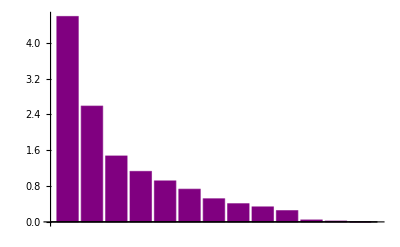

```mathematica
BarChart[varianceOfEachColumn1,ChartStyle->Purple]
```

```mathematica
(*the following function tells us how much of the total variance is accounted for after adding in each principal component. Like the authors, we find the first four principal components explain ~75% of the variance, and five principal components explain ~82%. So we agree that a five-variable regression function might be able to reliably predict the outcome...*)
```

```mathematica
cumulativeVariance1=Accumulate[varianceOfEachColumn1/Total@varianceOfEachColumn1]
```

{0.352978,0.551977,0.665276,0.752026,0.822506,0.878724,0.918507,0.949825,0.975666,0.99508,0.998454,1.,1.}

```mathematica
(*to overlay the two graphs like in the paper, we find we have to reduce the heights of the barchart columns. Anyway, the point is made:*)
```

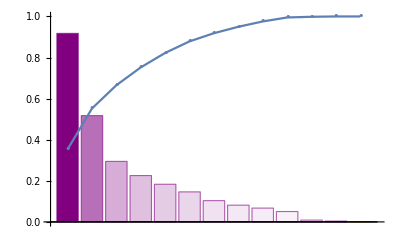

```mathematica
Show[{BarChart[1/5varianceOfEachColumn1,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance1,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

This could be used to compute optimized variables but the practical application of that would be unwieldy - we don’t want to have to compute all the original input descriptors every time we want to predict the activity of a new compound.

### Correlation Matrix

The following matrix is a table of Pearson’s correlation coefficients (r values) between each chemical measurement.
High inter-correlation between a pair of characteristics can distort a linear regression analysis, so the authors decided to avoid any pair of characteristics with an absolute value of r greater than 0.8. Only refractive index (n) and surface tension (γ) had such a high inter-correlation; refractive index was therefore left out of the subsequent regression analysis.
Actual formula for correlation coefficient: Correl(X,Y) = [Sum((x-xbar)(y-ybar))]/[SqRt[(Sum(x-xbar)^2)(Sum(y-ybar)^2)]] where xbar and ybar are the averages of the data set for the respective measurements.

```mathematica
Correlation[actualData4]//MatrixForm
```

(1. | -0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.259118 | -0.352955 | 0.196377 | 0.342209 | 0.0539286 | -0.0293615 | 0.199581 | 0.531941
-0.445075 | 1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | -0.294584 | 0.33373 | -0.251888 | -0.526888 | -0.351307 | -0.194399 | -0.74975 | -0.202031
-0.264673 | -0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0570004 | 0.0222463 | 0.0328363 | -0.279507 | 0.0631735 | -0.0262394 | 0.0985546 | -0.246192
0.37217 | 0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.269334 | -0.0991034 | -0.208526 | 0.0429598 | -0.150405 | -0.0484502 | -0.239614 | 0.395812
-0.577815 | 0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | -0.120574 | 0.605684 | -0.14666 | -0.430435 | -0.396205 | -0.383033 | -0.126844 | -0.509443
-0.333557 | 0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | -0.432335 | 0.653866 | -0.401401 | -0.493919 | -0.652339 | -0.52948 | -0.408954 | -0.223622
-0.259118 | -0.294584 | 0.0570004 | -0.269334 | -0.120574 | -0.432335 | 1. | -0.307771 | 0.0261029 | 0.313594 | 0.250516 | 0.201145 | 0.0827052 | -0.11172
-0.352955 | 0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | -0.307771 | 1. | -0.167066 | -0.325735 | -0.370674 | -0.309641 | -0.110675 | -0.392581
0.196377 | -0.251888 | 0.0328363 | -0.208526 | -0.14666 | -0.401401 | 0.0261029 | -0.167066 | 1. | 0.0568898 | 0.467254 | 0.426957 | 0.334716 | 0.0524229
0.342209 | -0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | 0.313594 | -0.325735 | 0.0568898 | 1. | 0.198254 | 0.164145 | 0.290585 | 0.323211
0.0539286 | -0.351307 | 0.0631735 | -0.150405 | -0.396205 | -0.652339 | 0.250516 | -0.370674 | 0.467254 | 0.198254 | 1. | 0.951168 | 0.627186 | 0.176771
-0.0293615 | -0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | 0.201145 | -0.309641 | 0.426957 | 0.164145 | 0.951168 | 1. | 0.578043 | 0.116499
0.199581 | -0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | 0.0827052 | -0.110675 | 0.334716 | 0.290585 | 0.627186 | 0.578043 | 1. | 0.0434568
0.531941 | -0.202031 | -0.246192 | 0.395812 | -0.509443 | -0.223622 | -0.11172 | -0.392581 | 0.0524229 | 0.323211 | 0.176771 | 0.116499 | 0.0434568 | 1.)

```mathematica
TableForm[%70]
```

1. | -0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.259118 | -0.352955 | 0.196377 | 0.342209 | 0.0539286 | -0.0293615 | 0.199581 | 0.531941
-0.445075 | 1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | -0.294584 | 0.33373 | -0.251888 | -0.526888 | -0.351307 | -0.194399 | -0.74975 | -0.202031
-0.264673 | -0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0570004 | 0.0222463 | 0.0328363 | -0.279507 | 0.0631735 | -0.0262394 | 0.0985546 | -0.246192
0.37217 | 0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.269334 | -0.0991034 | -0.208526 | 0.0429598 | -0.150405 | -0.0484502 | -0.239614 | 0.395812
-0.577815 | 0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | -0.120574 | 0.605684 | -0.14666 | -0.430435 | -0.396205 | -0.383033 | -0.126844 | -0.509443
-0.333557 | 0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | -0.432335 | 0.653866 | -0.401401 | -0.493919 | -0.652339 | -0.52948 | -0.408954 | -0.223622
-0.259118 | -0.294584 | 0.0570004 | -0.269334 | -0.120574 | -0.432335 | 1. | -0.307771 | 0.0261029 | 0.313594 | 0.250516 | 0.201145 | 0.0827052 | -0.11172
-0.352955 | 0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | -0.307771 | 1. | -0.167066 | -0.325735 | -0.370674 | -0.309641 | -0.110675 | -0.392581
0.196377 | -0.251888 | 0.0328363 | -0.208526 | -0.14666 | -0.401401 | 0.0261029 | -0.167066 | 1. | 0.0568898 | 0.467254 | 0.426957 | 0.334716 | 0.0524229
0.342209 | -0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | 0.313594 | -0.325735 | 0.0568898 | 1. | 0.198254 | 0.164145 | 0.290585 | 0.323211
0.0539286 | -0.351307 | 0.0631735 | -0.150405 | -0.396205 | -0.652339 | 0.250516 | -0.370674 | 0.467254 | 0.198254 | 1. | 0.951168 | 0.627186 | 0.176771
-0.0293615 | -0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | 0.201145 | -0.309641 | 0.426957 | 0.164145 | 0.951168 | 1. | 0.578043 | 0.116499
0.199581 | -0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | 0.0827052 | -0.110675 | 0.334716 | 0.290585 | 0.627186 | 0.578043 | 1. | 0.0434568
0.531941 | -0.202031 | -0.246192 | 0.395812 | -0.509443 | -0.223622 | -0.11172 | -0.392581 | 0.0524229 | 0.323211 | 0.176771 | 0.116499 | 0.0434568 | 1.

We find again that n and γ are too highly correlated (R=0.951). Like the authors, we drop n.

```mathematica
(*drop -4th column*)
goodData1=ReplacePart[actualData4,{_,-4}->Nothing];
```

### Multiple Linear Regression Analysis

The purpose of the following analysis is to recapitulate the linear models in the Aouidate, et al paper.

```mathematica
(*map applies an operation to every row. Here we want to move the first column (which contains the response variable logUM) to the end*)
reformatted12=Map[Flatten@{#[[2;;-1]],#[[1]]}&,goodData1];
```

```mathematica
(*Now I will first try a linear model with all 12 descriptors*)
```

```mathematica
model12=LinearModelFit[reformatted12,Table[x[i],{i,1,12}],Table[x[i],{i,1,12}]]
```

FittedModel[«15»+0.00121584 x[9]-0.0410994 x[10]-0.55746 x[11]+0.0802493 x[12]]

```mathematica
model12["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
model12["RSquared"]
```

0.722616

### Linear Regression with the Five Variables Aouidate, et al Recommend

```mathematica
recommendedData1=reformatted12[[All,{1,3,5,6,10,-1}]];
```

```mathematica
model5=LinearModelFit[recommendedData1,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]
```

FittedModel[10.4527-0.0000216893 x[1]+1.39137 x[2]-1.53798 x[3]-0.260324 x[4]-0.040324 x[5]]

```mathematica
model5["BestFitParameters"]
```

{10.4527,-0.0000216893,1.39137,-1.53798,-0.260324,-0.040324}

```mathematica
model5["RSquared"]
```

0.674987

Our linear RSquared is a bit lower than the authors’. That’s interesting.

### Non-Linear Regression

```mathematica
nonlinear5=NonlinearModelFit[
recommendedData1,
a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}
]
```

FittedModel[90.3671-0.000091531 x1-6.87724×10^-10 x1^2+22.0414 x2+«19» x2^2-«1»+«18» «1»-0.301465 x4-0.00106867 x4^2-1.37504 x5+0.0165701 x5^2]

```mathematica
nonlinear5["BestFitParameters"]
```

{a→90.3671,b→-0.000091531,c→22.0414,d→-3.77805,e→-0.301465,f→-1.37504,g→-6.87724×10^-10,h→1.94603,n→6.52962,m→-0.00106867,k→0.0165701}

```mathematica
nonlinear5["RSquared"]
```

0.932038

Our non-linear RSquared is fantastic, and higher than the authors’. That’s suspicious and also interesting.

### External Validation

I will randomly select 35 of the 46 compounds to train a similar non-linear model fit, then see how well it does predicting the log(UM)’s of the rest.

```mathematica
TakeDrop[RandomSample[{1,2,3,4,5}],2]
```

{{2,5},{4,1,3}}

```mathematica
(*Magic incantation to split the data: Set a list of two names (training and testing) equal to a function, the output of which is a list of two lists. The two lists are a random sample of the data with the specified length and then the rest of the data*)
```

```mathematica
{training,testing}=TakeDrop[RandomSample[recommendedData1],35];
```

```mathematica
Dimensions[testing]
```

{11,6}

```mathematica
Dimensions[training]
```

{35,6}

```mathematica
nonlinear5and35 = NonlinearModelFit[
training,
a+b x1+c x2+d x3+e x4+f x5+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2,{a,b,c,d,e,f,g,h,n,m,k},
{x1,x2,x3,x4,x5}
]
```

FittedModel[105.955-0.000111238 x1-8.1458×10^-10 x1^2+26.4566 x2+«19» x2^2-«1»+«18» «1»-0.464663 x4+0.0331275 x4^2-1.59004 x5+0.0191646 x5^2]

```mathematica
nonlinear5and35["RSquared"]
```

0.945245

```mathematica
observed=testing[[All,-1]]
```

{0.58,1.27,0.83,0.86,1.,1.25,1.95,1.69,-0.06,0.38,1.}

```mathematica
predicted=Map[
nonlinear5and35["BestFit"]/.Thread[{x1,x2,x3,x4,x5,output}->#]&,
testing
]
```

{1.13911,0.82894,0.426561,1.37547,1.03543,1.4016,1.83253,2.43951,0.047784,0.911016,0.429587}

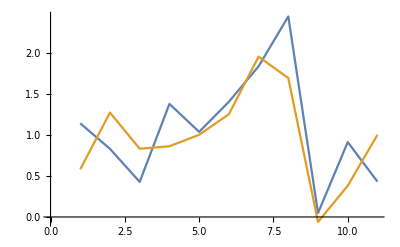

```mathematica
ListLinePlot[{predicted,observed}]
```

```mathematica
combinedData=Transpose[{predicted,observed}]
```

{{1.13911,0.58},{0.82894,1.27},{0.426561,0.83},{1.37547,0.86},{1.03543,1.},{1.4016,1.25},{1.83253,1.95},{2.43951,1.69},{0.047784,-0.06},{0.911016,0.38},{0.429587,1.}}

```mathematica
(*what follows is a scatter plot with observed values on the y axis and predicted on the x*)
```

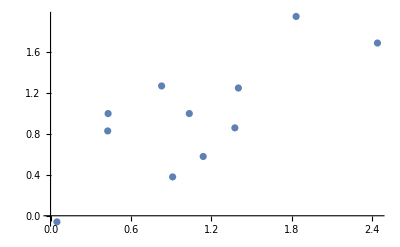

```mathematica
testlistplot=ListPlot@combinedData
```

```mathematica
fit=LinearModelFit[combinedData,x,x]
```

FittedModel[0.297618+0.629972 x]

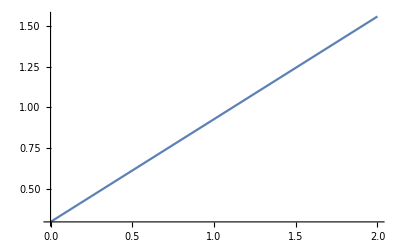

```mathematica
linePlot=Plot[fit["BestFit"],{x,0,2}]
```

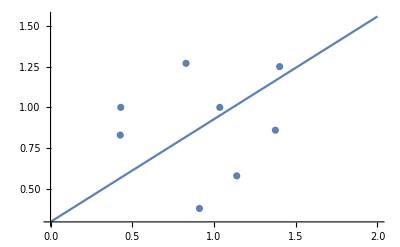

```mathematica
Show[linePlot,testlistplot]
```

```mathematica
(*R-Squared value of the above plot*)
```

```mathematica
fit["RSquared"]
```

0.565422

```mathematica
(*Pearson's correlation coefficient of the resulting list of predicted and observed values*)
```

```mathematica
Correlation[combinedData]
```

{{1.,0.751946},{0.751946,1.}}

Even knowing that predicted and observed vary in the same direction 80% of the time would be useful to chemists in the real world - we usually take qualitative information from these models and use it to optimize structure.

Future goals: Recapitulate the backwards linear regression to validate that the selected five variables really are the best set to predict activity. The authors claim that when they did backwards linear regression from a model with all 12 descriptors (a mix of physicochemical things like logP, MW, etc and electronic descriptors like Ehomo, absolute hardness) the best linear fit was the five variables used above (Etotal, Ehomo, Elumo, absolute hardness and surface tension). We could validate that that’s true by generating the R^2’s of linear fit of all 12c5 = 792 possible combinations.

### “Backwards” Linear Regression

Here by “backwards” regression we mean testing linear model fits from matrices of smaller subsets of the descriptors and the response variable logUM. In this case we will try five-variable design matrices because the PCA analysis indicates five variables may suffice to model this data. From 12 variables, there are 792 different combinations of five. Aouidate, et al claim that the best fit was with the aforementioned five variables of Etotal, Ehomo, Elumo, absolute hardness and surface tension. I want to check/verify that and I also want to know what the runners-up were.

```mathematica
(*What follows is the development of an algorith. Work largely by Dr. Keane*)
```

```mathematica
whichParameters=Subsets[Range[Length@First@reformatted12-1],{5}];
```

```mathematica
Length[whichParameters]
```

792

```mathematica
(*by eye and by showing that the list contains 12c5=792 combos, I think the function above is correct*)
```

```mathematica
whichParameters2=Append[#,-1]&/@whichParameters;
```

```mathematica
Length[whichParameters2]
```

792

```mathematica
parameters=whichParameters2[[1]]
```

{1,2,3,4,5,-1}

```mathematica
(*confirmed, that's the first member of the list*)
```

```mathematica
regressThese=Part[reformatted12,All,parameters];
```

```mathematica
Length[regressThese]
```

```mathematica
46
```

```mathematica
(*Confirmed that the output of "regressThese" is a list of 46 lists, where each list is the values of the first five descriptors, then logUM, for each compound*)

(*If I understand correctly, what follows is a linear model fit in which the design matrix is the first five columns of regressThese and the response vector is the (-1) column?*)
```

```mathematica
LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
```

0.488425

```mathematica
(*Assuming everything's written right, that means the first variable set, columns 1-5 {ET IP EHOMO η ELUMO DM} has an R^2 of 0.488425?*)
```

```mathematica
allRSquared=MapIndexed[
Function[
{parameters,index},
regressThese=Part[reformatted12,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
],
whichParameters2
];
```

```mathematica
(*Here's the most important place to be sure I understand what's going on. Before we defined "parameters" as the first entry of "whichParameters2", but here we are repeating the function for all possible values of "parameters", corresponding to every entry in whichParameters2. We're then taking those values of "parameters" and using them to create the 792 different values of regressThese, each a matrix in the format [design matrix | response vector]. Then we're running a linear model fit for each value of regressThese and spitting out the RSquared value. Right?*)
```

```mathematica
Length[allRSquared]
```

792

```mathematica
(*confirmed the length of the output is 792*)
```

```mathematica
bestFits=TakeLargestBy[allRSquared,Last,UpTo[5]]
```

{239→0.692559,232→0.691919,240→0.689036,233→0.684371,238→0.68246}

```mathematica
(*Below, will find out which sets of variables correspond to the five best RSquared values above. Here's where things get interesting!*)
```

```mathematica
whichParameters2[[239]]
```

{1,4,6,10,12,-1}

```mathematica
whichParameters2[[232]]
```

{1,4,6,8,10,-1}

```mathematica
whichParameters2[[240]]
```

{1,4,6,11,12,-1}

```mathematica
whichParameters2[[233]]
```

{1,4,6,8,11,-1}

```mathematica
whichParameters2[[238]]
```

{1,4,6,10,11,-1}

Analysis:
Yikes, I think I'm getting a different result from the author that' s interesting in a couple ways. Those linear fits are almost identical RSquared' s. 1, 4, and 6 are Etotal, absolute hardness, and dipole moment respectively; 10, 11 and 12 are surface tension, density and logP; 8 is Qmin, the most negative net atomic charge, which is also from DFT but did not factor into the final models in the original paper at all!
I used the Find command to find the entry in the output of the AllRSquared function above, with a RSquared value to match the earlier five-variable linear model fit. It's entry #152. Below, I use the whichParameters2 function to find the column numbers corresponding to that output. Those column numbers indeed match the variables from the five-variable linear model in the Aouidate paper, the same model we recapitulated earlier in this project. That gives me more certainty of the analysis above.
What Madeleine thinks: Absolute hardness (η) is the only DFT descriptor, and (calculated) logP the only physicochemical descriptor, with an absolute value of the Pearson’s correlation coefficient with logUM greater than 0.5, interpreted to mean moving together with logUM more than half the time, so it makes sense that those two descriptors would show up in the best linear model fits. Aouidate, et al were not terribly clear about how they defined “best linear fit” so I went with RSquared for now and noted that the RSquared’s for the top hits above and the model with Aouidate, et al’s recommended descriptors are within 2% of each other. I think an interesting future direction would be to 1) explore what other descriptors I can get out of a DFT structure... HOMO orbital coefficient at an atom involved in a key interaction for a set of compounds of interest?? 2) Repeat this analysis with more biochemically relevant, and possibly empirical, physicochemical descriptors and see if the DFT descriptors still win out/end up being highly represented in the best fit.

```mathematica
whichParameters2[[152]]
```

{1,3,5,6,10,-1}